# Lab 6 : Max/Min Problems

## 1. [Lagrange Multipliers] Find the max/min of f(x,y)=y-x^3 subject to the constraint x^4+x y-y^2+y^4=2. Let's make a plot of the constraint; note that it is a closed loop.

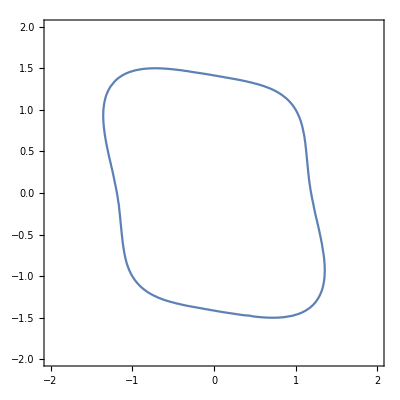

```mathematica
constraintplot=ContourPlot[x^4+x y-y^2+y^4==2,{x,-2,2},{y,-2,2}]
```

Next, let' s make a contour map plot of  f(x,y).

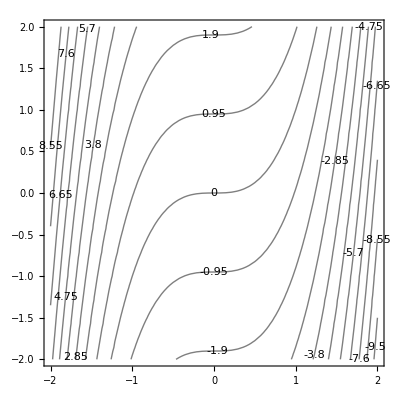

```mathematica
plot2=ContourPlot[y-x^3,{x,-2,2},{y,-2,2},Contours->20,ContourShading->False,ContourLabels->True]
```

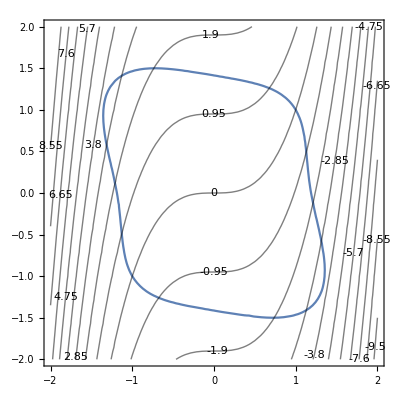

```mathematica
Show[constraintplot,plot2]
```

From looking at the above, where would you guess is the max and min? (Just a guess.)

#### Response:

Now let us solve the Lagrange multiplier system.  We will use the numerical solve command NSolve because the system is not algebraically solvable.  For example, the following finds the critical points for finding max/min of  x+2y  on constraint x^4+y^2=1.

```mathematica
exampleCriticalPoints=NSolve[{(1)==λ*(4x^3),(2)==λ*(2y),x^4+y^2==1},{x,y,λ},Reals]
```

Use the following template to fill in your own command in place of the dots.  Note the double equal signs!

```mathematica
criticalPoints=NSolve[{(...)==λ*(...),(...)==λ*(...),x^4+x y-y^2+y^4==2},{x,y,λ},Reals]
```

The following command evaluates the optimization function at the critical points.

```mathematica
y-x^3/.criticalPoints
```

ReplaceAll::reps: {criticalPoints} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-x^3+y/.criticalPoints

Looking at the  solutions, do they agree with your guesses?  Which is the max and which is the min?

#### Response:

## 2. In this problem, we will use contour maps to find absolute extrema for us. We will search for the absolute maximum and absolute minimum of the function f(x,y)=y-x^2 on various domains. Let us look at the contour map of this function to get a good feel for it.

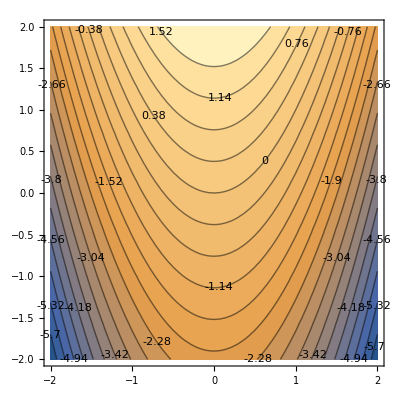

```mathematica
cmap=ContourPlot[y-x^2,{x,-2,2},{y,-2,2},Contours->20,ContourLabels->True]
```

Execute the following command to obtain two domains along with the above contour map.

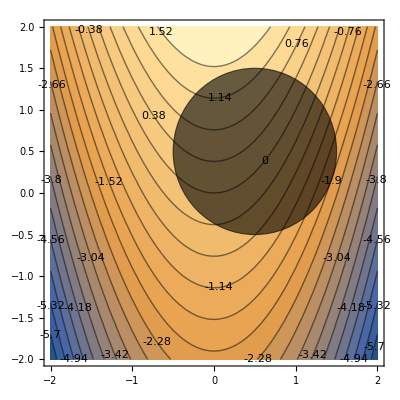

```mathematica
Show[cmap,Graphics[{EdgeForm[Thick],Opacity[0.6],Disk[{.5,.5},1]}]]
```

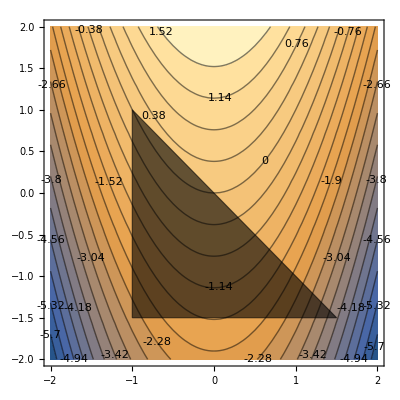

```mathematica
Show[cmap,Graphics[{EdgeForm[Thick],Opacity[0.6],Triangle[{{-1,-1.5},{-1,1},{1.5,-1.5},{-1,-1.5}}]}]]
```

Give approximate coordinates for where the maximum and minimum of f (x, y) occur in the above domains  (The first domain is the circle and its inside; the second domain is the triangle and its inside.) 
Hint : find the point (s) where the interaction with the contours is such that you maximize or minimize the function.

#### Response for circle domain:

#### Response for triangle domain: